Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_348291.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/21,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{165.613,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{475.779,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,11,win2];]
```

{148.873,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{543.587,Null}

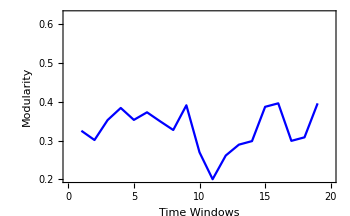
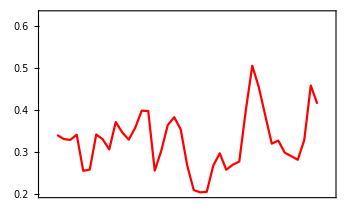
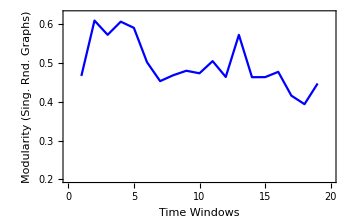
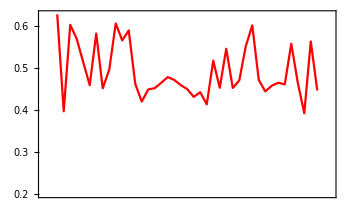
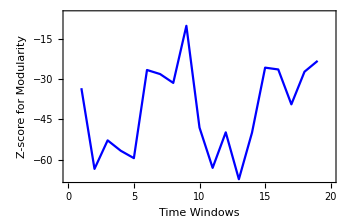
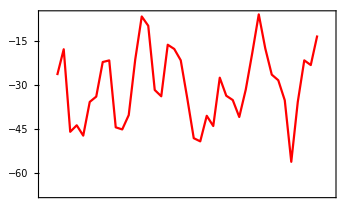

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,1,win1];]
```

{21.83,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{149.262,Null}

```mathematica
N@Mean@graphsandnodenumbers[[All,2]]
```

19.3158

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,1,win2];]
```

{20.2073,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{277.792,Null}

```mathematica
N@Mean@graphsandnodenumbers[[All,2]]
```

13.8293

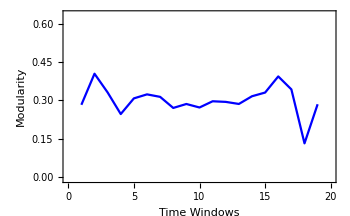
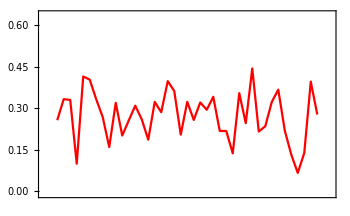
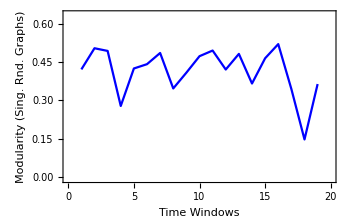
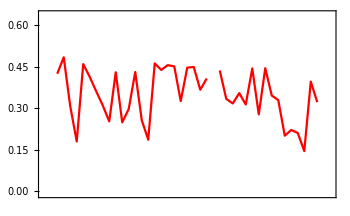
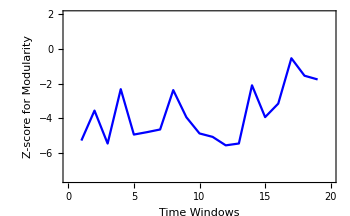
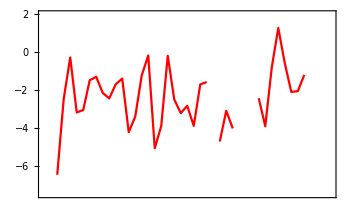

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-7.5,2}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-7.5,2}}]}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,85,win1];]
```

{12.1416,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{397.487,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,70,win2];]
```

{19.957,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{851.007,Null}

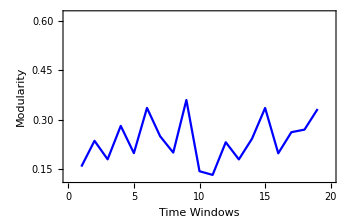
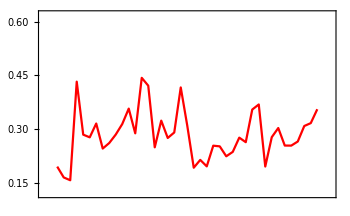
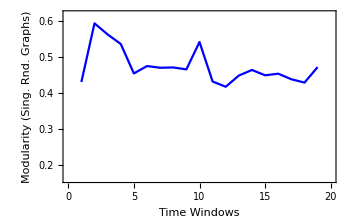
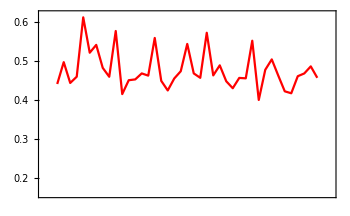
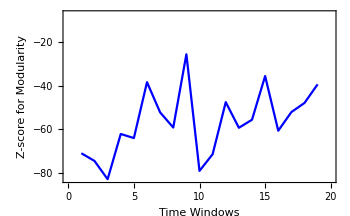
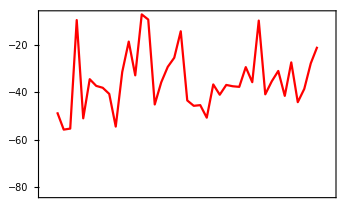

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.12,0.62}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.12,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.16,0.62}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.16,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,20,win1];]
```

{14.1616,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{184.494,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,14,win2];]
```

{10.7265,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{328.042,Null}

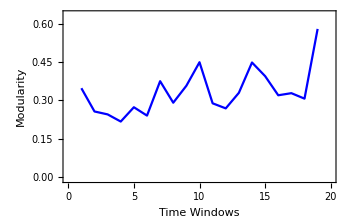
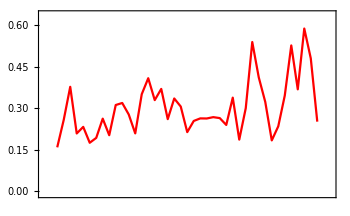
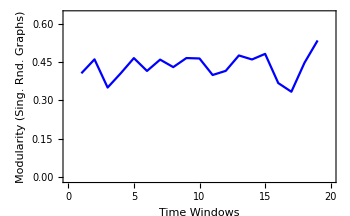
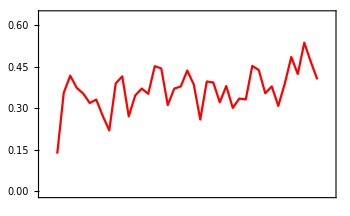
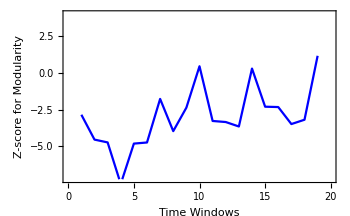
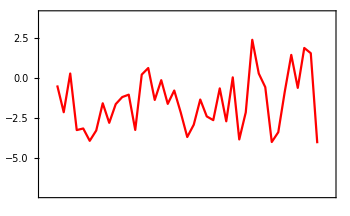

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-7.25,4}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-7.25,4}}]}]}
```